```mathematica
Collect[Series[-2/r+Exp[-α r](Subscript[c, 0]/r+Subscript[c, 1]),{r,0,2}],r,FullSimplify]
```

(-2+c_0)/r-α c_0-1/6 r^2 α^2 (α c_0-3 c_1)+1/2 r α (α c_0-2 c_1)+c_1

```mathematica
Collect[Series[-2/r+Exp[-α r](2/r+2α-Subscript[U, c]),{r,0,2}],r,FullSimplify]
```

1/6 r^2 α^2 (4 α-3 U_c)-U_c+r α (-α+U_c)

```mathematica
Collect[Series[-2/r+Exp[-Subscript[U, c] r](2/r+Subscript[U, c]),{r,0,2}],r,FullSimplify]
```

-U_c+1/6 r^2 U_c^3

```mathematica
f[𝒩_]:=Sum[Subscript[c,n] r^(n-1),{n,0,𝒩+1}]
Collect[Series[-2/r+Exp[-α r]f[30],{r,0,2}],r,FullSimplify]
Block[{rules},
rules={Subscript[c, 0]->2,Subscript[c, 1]->2α-Subscript[U, c],Subscript[c, 2]->1/2 α(2α-2 Subscript[U, c]),Subscript[c, 3]->1/6 α^2(2α-3 Subscript[U, c]),Subscript[c, 4]->1/24 α^3(2α-4 Subscript[U, c])};
Collect[Series[-2/r+Exp[-α r]f[30],{r,0,4}]/.rules,r,FullSimplify]
]
Clear[f];
```

(-2+c_0)/r-α c_0+c_1+r ((α^2 c_0)/2-α c_1+c_2)+r^2 (-1/6 α (α^2 c_0-3 α c_1+6 c_2)+c_3)

-U_c+r^4 (c_5+1/120 α^4 (-2 α+5 U_c))

```mathematica
f[𝒩_]:=Sum[(2α Subscript[U, c]-n Subscript[U, c])(α Subscript[U, c] r)^(n-1)/(n!),{n,0,𝒩-1}]
Collect[Series[-2/r+Exp[-α Subscript[U, c] r]f[21],{r,0,21}],r,FullSimplify]
Clear[f];
```

-U_c+(r^20 (21-2 α) α^20 U_c^21)/51090942171709440000+(r^21 α^21 (-220+21 α) U_c^22)/562000363888803840000

```mathematica
Block[{f,g,𝒩=21},
f=Sum[(𝒩 Subscript[U, c]-n Subscript[U, c])(𝒩/2 Subscript[U, c] r)^(n-1)/(n!),{n,0,𝒩-1}];
g=-2/r+Exp[-𝒩/2 Subscript[U, c] r]f;
Collect[Series[g,{r,0,𝒩}],r,FullSimplify]
]
```

-U_c+(865405750887126927009 r^21 U_c^22)/349149230205501440000

```mathematica
f[𝒩_]:=Subscript[U, c] Sum[(2α Subscript[c,n]-n)(α Subscript[U, c] r)^(n-1)/(n!),{n,0,𝒩-1}]
Collect[Series[-2/r 𝓀[r]+Exp[-α Subscript[U, c] r]f[30],{r,0,2}],r,FullSimplify]
Block[{rules},
rules={Subscript[c, 0]->𝓀[0],Subscript[c, 1]->𝓀[0]+𝓀'[0]/(α Subscript[U, c]),Subscript[c, 2]->𝓀[0]+2 𝓀'[0]/(α Subscript[U, c])+𝓀''[0]/(α Subscript[U, c])^2,Subscript[c, 3]->𝓀[0]+3 𝓀'[0]/(α Subscript[U, c])+3 𝓀''[0]/(α Subscript[U, c])^2+ (Derivative[3][𝓀][0])/(α Subscript[U, c])^3,Subscript[c, 4]->𝓀[0]+4 𝓀'[0]/(α Subscript[U, c])+6 𝓀''[0]/(α Subscript[U, c])^2+ 4(Derivative[3][𝓀][0])/(α Subscript[U, c])^3+(Derivative[4][𝓀][0])/(α Subscript[U, c])^4};
Collect[Series[-2/r 𝓀[r]+Exp[-α Subscript[U, c] r]f[30],{r,0,4}]/.rules,r,Together]
]
Clear[f];
```

(-1-2 α c_0+2 α c_1) U_c+(2 (c_0-𝓀[0]))/r-2 𝓀'[0]+r (α^2 (c_0-2 c_1+c_2) U_c^2-𝓀''[0])+1/3 r^2 (α^3 (-c_0+3 c_1-3 c_2+c_3) U_c^3-𝓀^(3)[0])

-U_c+1/60 r^4 (α^5 c_5 U_c^5-α^5 U_c^5 𝓀[0]-5 α^4 U_c^4 𝓀'[0]-10 α^3 U_c^3 𝓀''[0]-10 α^2 U_c^2 𝓀^(3)[0]-5 α U_c 𝓀^(4)[0]-𝓀^(5)[0])

```mathematica
Block[{f,𝒩=5},
f=Subscript[U, c] Sum[(2α Sum[Binomial[n,i](D[𝓀[𝓇/(α Subscript[U, c])],{𝓇,i}]/.{𝓇->0}),{i,0,n}]-n)(α Subscript[U, c] r)^(n-1)/(n!),{n,0,𝒩-1}];
Collect[Series[-2/r 𝓀[r]+Exp[-α Subscript[U, c] r]f,{r,0,𝒩}],r,Together]//Print;
]
```

-U_c+1/120 r^4 (5 α^4 U_c^5-2 α^5 U_c^5 𝓀[0]-10 α^4 U_c^4 𝓀'[0]-20 α^3 U_c^3 𝓀''[0]-20 α^2 U_c^2 𝓀^(3)[0]-10 α U_c 𝓀^(4)[0]-2 𝓀^(5)[0])+1/360 r^5 (-12 α^5 U_c^6+5 α^6 U_c^6 𝓀[0]+24 α^5 U_c^5 𝓀'[0]+45 α^4 U_c^4 𝓀''[0]+40 α^3 U_c^3 𝓀^(3)[0]+15 α^2 U_c^2 𝓀^(4)[0]-𝓀^(6)[0])

```mathematica
Block[{f,expr,𝒩=5},
f=Subscript[U, c] Sum[(2α Sum[Binomial[n,i](D[𝓀[𝓇/(α Subscript[U, c])],{𝓇,i}]/.{𝓇->0}),{i,0,n}]-n)(α Subscript[U, c] r)^(n-1)/(n!),{n,0,𝒩-1}];
expr=-2/r 𝓀[r]+Exp[-α Subscript[U, c] r]f;
Collect[Series[expr,{r,0,𝒩-1}],r,Together]//Print;
]
```

-U_c+1/120 r^4 (5 α^4 U_c^5-2 α^5 U_c^5 𝓀[0]-10 α^4 U_c^4 𝓀'[0]-20 α^3 U_c^3 𝓀''[0]-20 α^2 U_c^2 𝓀^(3)[0]-10 α U_c 𝓀^(4)[0]-2 𝓀^(5)[0])

```mathematica
Block[{f,eqn,expr,𝒩},
Do[
f=Subscript[U, c] Sum[((𝒩 α)/𝓀[0] Sum[Binomial[n,i](D[𝓀[(2𝓀[0])/(𝒩 α Subscript[U, c])𝓇],{𝓇,i}]/.{𝓇->0}),{i,0,n}]-n)((𝒩 α)/(2𝓀[0]) Subscript[U, c] r)^(n-1)/(n!),{n,0,𝒩-1}];
expr=-2/r 𝓀[r]+Exp[-(𝒩 α)/(2𝓀[0]) Subscript[U, c] r]f;
eqn=(CoefficientList[Collect[Series[expr,{r,0,𝒩-1}],r,FullSimplify],r]//Last)==0;
Solve[eqn/.{Derivative[n_?((#>0)&)][𝓀][0]->0},α]//Print;
,{𝒩,2,5}]
]
```

{{α→0},{α→1}}

{{α→0},{α→0},{α→1}}

{{α→0},{α→0},{α→0},{α→1}}

{{α→0},{α→0},{α→0},{α→0},{α→1}}

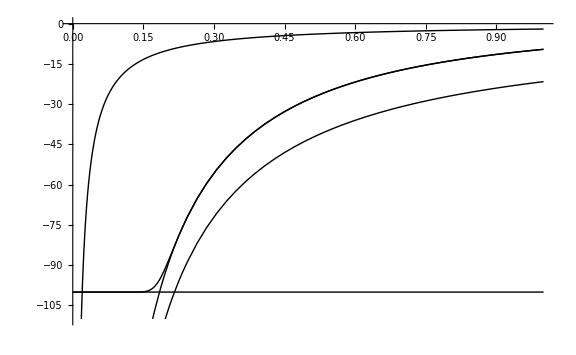
-Graphics-r/r_AUE/E_AU𝒩 = 101

```mathematica
Block[{
prec,Δ,
𝒩,Uc,
𝓀,rules,rule,n,
α,
f,g,
s,eqn,soln,
plt
},
prec=960;
Δ=SetPrecision[.1,prec];

𝒩=101;
Uc=SetPrecision[100.,prec];


rules=SetPrecision[{
{η->11.4,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->10.8,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->11.3,A->1.0000,  γ0->0.9500,γ1->0.0000,γ2->2.044},
{η->10.8,A->0.8918,γ0->0.9743,γ1->0.1586,γ2->0.1586}
},prec];
rule=rules[[4]];

f=Uc Sum[((𝒩 α)/𝓀[0] Sum[Binomial[n,i](D[𝓀[(2𝓀[0])/(𝒩 α Uc)𝓇],{𝓇,i}]/.{𝓇->0}),{i,0,n}]-n)((𝒩 α)/(2𝓀[0]) Uc r)^(n-1)/(n!),{n,0,𝒩-1}];
g=-2/r 𝓀[r]+Exp[-(𝒩 α)/(2𝓀[0]) Uc r]f;

s=Collect[Series[g,{r,0,𝒩}],r,Together];
eqn=Assuming[{Uc>0,𝓀[0]>0},
D[s,{r,𝒩-1}]/.r->0//FullSimplify
];
𝓀[r_]=1+A η Exp[-γ0 r]+(1-A)η Exp[-γ1 r]-Exp[-γ2 r]/.rule;
α=Select[Block[{x=Solve[eqn==0,α]},Table[x[[n,1]][[2]],{n,1,Length[x]}]]//Chop,Positive]//Max;

Off[General::munfl];
plt=Plot[
{
Style[-Uc,Dashed,Thickness[Medium],Red],Style[-2/r,DotDashed,Thickness[Medium],Darker[Green]],Style[-2/r 𝓀[0],DotDashed,Thickness[Medium],Blue]
,Style[g,Purple],Style[-2/r 𝓀[r],Orange,Thickness[Large]]
}
,{r,0,1}
,WorkingPrecision->prec-10,PerformanceGoal->"Quality",ImageSize->Large
,PlotRange->{(-1-Δ)Uc,0}];
Labeled[plt,{r/Subscript[r, AU],"E/E_AU","𝒩 = "<>ToString[𝒩]},{Top,Left,Bottom}]//Print;
On[General::munfl];
]
```

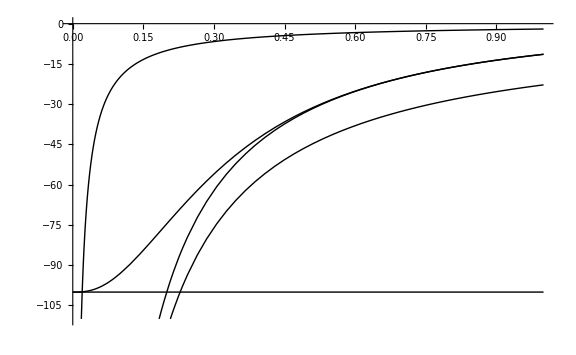
-Graphics-r/r_AUE/E_AU𝒩 = 3

```mathematica
Block[{
prec,Δ,
𝒩,Uc,
𝓀,rules,rule,n,
α,
f,g,
s,eqn,soln,
plt
},
prec=960;
Δ=SetPrecision[.1,prec];

𝒩=3;
Uc=SetPrecision[100.,prec];


rules=SetPrecision[{
{η->11.4,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->10.8,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->11.3,A->1.0000,  γ0->0.9500,γ1->0.0000,γ2->2.044},
{η->10.8,A->0.8918,γ0->0.9743,γ1->0.1586,γ2->0.1586}
},prec];
rule=rules[[1]];

f=Uc Sum[((𝒩 α)/𝓀[0] Sum[Binomial[n,i](D[𝓀[(2𝓀[0])/(𝒩 α Uc)𝓇],{𝓇,i}]/.{𝓇->0}),{i,0,n}]-n)((𝒩 α)/(2𝓀[0]) Uc r)^(n-1)/(n!),{n,0,𝒩-1}];
g=-2/r 𝓀[r]+Exp[-(𝒩 α)/(2𝓀[0]) Uc r]f;

s=Collect[Series[g,{r,0,𝒩}],r,Together];
eqn=Assuming[{Uc>0,𝓀[0]>0},
D[s,{r,𝒩-1}]/.r->0//FullSimplify
];
𝓀[r_]=1+A η Exp[-γ0 r]+(1-A)η Exp[-γ1 r]-Exp[-γ2 r]/.rule;
α=Select[Block[{x=Solve[eqn==0,α]},Table[x[[n,1]][[2]],{n,1,Length[x]}]]//Chop,Positive]//Max;

Off[General::munfl];
plt=Plot[
{
Style[-Uc,Dashed,Thickness[Medium],Red],Style[-2/r,DotDashed,Thickness[Medium],Darker[Green]],Style[-2/r 𝓀[0],DotDashed,Thickness[Medium],Blue]
,Style[g,Purple],Style[-2/r 𝓀[r],Orange,Thickness[Large]]
}
,{r,0,1}
,WorkingPrecision->prec-10,PerformanceGoal->"Quality",ImageSize->Large
,PlotRange->{(-1-Δ)Uc,0}];
Labeled[plt,{r/Subscript[r, AU],"E/E_AU","𝒩 = "<>ToString[𝒩]},{Top,Left,Bottom}]//Print;
On[General::munfl];
]
```

```mathematica
Block[{
prec,Δ,
𝒩,Uc,
𝓀,rules,rule,n,
α,
f,g,
s,eqn,soln,
plt
},
𝒩=3;

f=Uc Sum[((𝒩 α)/𝓀[0] Sum[Binomial[n,i](D[𝓀[(2𝓀[0])/(𝒩 α Uc)𝓇],{𝓇,i}]/.{𝓇->0}),{i,0,n}]-n)((𝒩 α)/(2𝓀[0]) Uc r)^(n-1)/(n!),{n,0,𝒩-1}];
g=-2/r 𝓀[r]+Exp[-(𝒩 α)/(2𝓀[0]) Uc r]f;

s=Collect[Series[g,{r,0,𝒩}],r,Together];
eqn=Assuming[{Uc>0,𝓀[0]>0,A>0,η>1},
(D[s,{r,𝒩-1}]/.r->0)==0//FullSimplify
];
𝓀[r_]=1+A η Exp[-γ0 r]+(1-A)η Exp[-γ1 r]-Exp[-γ2 r];


Collect[g,{Exp[_],r},FullSimplify]//Print;
Assuming[{α>0,Uc>0},Collect[eqn,α,Expand[FullSimplify[#]]&]]

]
```

-2/r+(2 ⅇ^(-r γ2))/r-(2 A ⅇ^(-r γ0) η)/r+(2 (-1+A) ⅇ^(-r γ1) η)/r+ⅇ^(-(3 r Uc α)/(2 ((1-A) η+A η))) (Uc (-1+3 α)+2 γ2+(2 η)/r-2 (A γ0+γ1-A γ1) η+r (-3 Uc α γ1-γ2^2+(3 Uc α (Uc (-2+3 α)+4 γ2))/(4 η)+γ1^2 η+A (γ0-γ1) (-3 Uc α+(γ0+γ1) η)))

27 Uc^3 α^3+8 γ2^3 η^2-8 A γ0^3 η^3-8 γ1^3 η^3+8 A γ1^3 η^3+α^2 (-27 Uc^3+54 Uc^2 γ2-54 A Uc^2 γ0 η-54 Uc^2 γ1 η+54 A Uc^2 γ1 η)+α (-36 Uc γ2^2 η+36 A Uc γ0^2 η^2+36 Uc γ1^2 η^2-36 A Uc γ1^2 η^2)==0

```mathematica
Block[{
prec,Δ,
𝒩,Uc,
𝓀,rules,rule,n,
α,
f,g,
s,eqn,soln,
plt
},
𝒩=3;

f=Uc Sum[2((𝒩 α)/(2𝓀[0]Uc) Sum[Binomial[n,i](D[𝓀[(2𝓀[0])/(𝒩 α)𝓇],{𝓇,i}]/.{𝓇->0}),{i,0,n}]-n)((𝒩 α)/(2𝓀[0]) r)^(n-1)/(n!),{n,0,𝒩-1}];
g=-2/r 𝓀[r]+Exp[-(𝒩 α)/(2𝓀[0]) r]f;

s=Collect[Series[g,{r,0,𝒩}],r,Together];
eqn=Assuming[{Uc>0,𝓀[0]>0,A>0,η>1},
(D[s,{r,𝒩-1}]/.r->0)==0//FullSimplify
];
𝓀[r_]=1+A η Exp[-γ0 r]+(1-A)η Exp[-γ1 r]-Exp[-γ2 r];


Collect[g,{Exp[_],r},FullSimplify]//Print;
Assuming[{α>0,Uc>0},Collect[eqn,α,Expand[FullSimplify[#]]&]]

]
```

-2/r+(2 ⅇ^(-r γ2))/r-(2 A ⅇ^(-r γ0) η)/r+(2 (-1+A) ⅇ^(-r γ1) η)/r+ⅇ^(-(3 r α)/(2 ((1-A) η+A η))) (-2 Uc+3 α+2 γ2+(2 η)/r-2 (A γ0+γ1-A γ1) η+r (-3 α (A (γ0-γ1)+γ1)-γ2^2+(3 α (-4 Uc+3 α+4 γ2))/(4 η)+(γ1^2+A (γ0-γ1) (γ0+γ1)) η))

27 α^3+8 γ2^3 η^2-8 A γ0^3 η^3-8 γ1^3 η^3+8 A γ1^3 η^3+α^2 (-54 Uc+54 γ2-54 A γ0 η-54 γ1 η+54 A γ1 η)+α (-36 γ2^2 η+36 A γ0^2 η^2+36 γ1^2 η^2-36 A γ1^2 η^2)==0

```mathematica
Block[{eqn},
eqn=27 Uc^3 α^3+8 γ2^3 η^2-8 A γ0^3 η^3-8 γ1^3 η^3+8 A γ1^3 η^3+α^2 (-27 Uc^3+54 Uc^2 γ2-54 A Uc^2 γ0 η-54 Uc^2 γ1 η+54 A Uc^2 γ1 η)+α (-36 Uc γ2^2 η+36 A Uc γ0^2 η^2+36 Uc γ1^2 η^2-36 A Uc γ1^2 η^2)==0/.Uc->1/u;
Assuming[{α>0,u>0},Collect[eqn,α,Expand[FullSimplify[#]]&]]
]
```

(27 α^3)/u^3+8 γ2^3 η^2-8 A γ0^3 η^3-8 γ1^3 η^3+8 A γ1^3 η^3+α^2 (-27/u^3+(54 γ2)/u^2-(54 A γ0 η)/u^2-(54 γ1 η)/u^2+(54 A γ1 η)/u^2)+α (-(36 γ2^2 η)/u+(36 A γ0^2 η^2)/u+(36 γ1^2 η^2)/u-(36 A γ1^2 η^2)/u)==0

```mathematica
Assuming[{α>0,Uc>0},Collect[27 Uc^3 α^3+8 γ2^3 η^2-8 A γ0^3 η^3-8 γ1^3 η^3+8 A γ1^3 η^3+α^2 (-27 Uc^3+54 Uc^2 γ2-54 A Uc^2 γ0 η-54 Uc^2 γ1 η+54 A Uc^2 γ1 η)+α (-36 Uc γ2^2 η+36 A Uc γ0^2 η^2+36 Uc γ1^2 η^2-36 A Uc γ1^2 η^2)==0/.α->α+1,α,Expand[FullSimplify[#]]&]]
```

27 Uc^3 α^3+54 Uc^2 γ2-54 A Uc^2 γ0 η-54 Uc^2 γ1 η+54 A Uc^2 γ1 η-36 Uc γ2^2 η+36 A Uc γ0^2 η^2+36 Uc γ1^2 η^2-36 A Uc γ1^2 η^2+8 γ2^3 η^2-8 A γ0^3 η^3-8 γ1^3 η^3+8 A γ1^3 η^3+α^2 (54 Uc^3+54 Uc^2 γ2-54 A Uc^2 γ0 η-54 Uc^2 γ1 η+54 A Uc^2 γ1 η)+α (27 Uc^3+108 Uc^2 γ2-108 A Uc^2 γ0 η-108 Uc^2 γ1 η+108 A Uc^2 γ1 η-36 Uc γ2^2 η+36 A Uc γ0^2 η^2+36 Uc γ1^2 η^2-36 A Uc γ1^2 η^2)==0

```mathematica
27 Uc^3 α^3+54 Uc^2 γ2-54 A Uc^2 γ0 η-54 Uc^2 γ1 η+54 A Uc^2 γ1 η-36 Uc γ2^2 η+36 A Uc γ0^2 η^2+36 Uc γ1^2 η^2-36 A Uc γ1^2 η^2+8 γ2^3 η^2-8 A γ0^3 η^3-8 γ1^3 η^3+8 A γ1^3 η^3+α^2 (54 Uc^3+54 Uc^2 γ2-54 A Uc^2 γ0 η-54 Uc^2 γ1 η+54 A Uc^2 γ1 η)+α (27 Uc^3+108 Uc^2 γ2-108 A Uc^2 γ0 η-108 Uc^2 γ1 η+108 A Uc^2 γ1 η-36 Uc γ2^2 η+36 A Uc γ0^2 η^2+36 Uc γ1^2 η^2-36 A Uc γ1^2 η^2)==0/.{
{η->11.4,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->10.8,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->11.3,A->1.0000,  γ0->0.9500,γ1->0.0000,γ2->2.044},
{η->10.8,A->0.8918,γ0->0.9743,γ1->0.1586,γ2->0.1586}
}
```

{2901.91+1352.22 Uc-402.608 Uc^2+(1352.22 Uc-805.216 Uc^2+27 Uc^3) α+(-402.608 Uc^2+54 Uc^3) α^2+27 Uc^3 α^3==0,2886.81+1128.13 Uc-375.609 Uc^2+(1128.13 Uc-751.218 Uc^2+27 Uc^3) α+(-375.609 Uc^2+54 Uc^3) α^2+27 Uc^3 α^3==0,-1173.35+2449.06 Uc-469.314 Uc^2+(0.+2449.06 Uc-938.628 Uc^2+27 Uc^3) α+(0.-469.314 Uc^2+54 Uc^3) α^2+27 Uc^3 α^3==0,-8312.65+3556.35 Uc-508.175 Uc^2+(3556.35 Uc-1016.35 Uc^2+27 Uc^3) α+(-508.175 Uc^2+54 Uc^3) α^2+27 Uc^3 α^3==0}

```mathematica
Assuming[{η>0,γ0>0,γ1>0,γ2>0},8 γ2^3 η^2-8 A γ0^3 η^3-8 γ1^3 η^3+8 A γ1^3 η^3==0//FullSimplify
]
```

γ2^3==(γ1^3+A (γ0^3-γ1^3)) η

```mathematica
Block[{
prec,Δ,
𝒩,Uc,
𝓀,rules,rule,n,
α,
f,g,
s,eqn,soln,
plt
},
𝒩=3;

prec=5;
rules=SetPrecision[{
{η->11.4,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->10.8,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->11.3,A->1.0000,  γ0->0.9500,γ1->0.0000,γ2->2.044},
{η->10.8,A->0.8918,γ0->0.9743,γ1->0.1586,γ2->0.1586}
},prec];
rule=rules[[1]];

f=Uc Sum[((𝒩 α)/𝓀[0] Sum[Binomial[n,i](D[𝓀[(2𝓀[0])/(𝒩 α Uc)𝓇],{𝓇,i}]/.{𝓇->0}),{i,0,n}]-n)((𝒩 α)/(2𝓀[0]) Uc r)^(n-1)/(n!),{n,0,𝒩-1}];
g=-2/r 𝓀[r]+Exp[-(𝒩 α)/(2𝓀[0]) Uc r]f;

s=Collect[Series[g,{r,0,𝒩}],r,Together];
eqn=Assuming[{Uc>0,𝓀[0]>0,A>0,η>1},
(D[s,{r,𝒩-1}]/.r->0)==0//FullSimplify
];
𝓀[r_]=1+A η Exp[-γ0 r]+(1-A)η Exp[-γ1 r]-Exp[-γ2 r];


Collect[g/.rule,{Exp[_],r},FullSimplify]//Print;
Collect[eqn/.rule,α,Expand[FullSimplify[#]]&]//Print;

]
```

-2/r+(2 ⅇ^(-2.044 r))/r-(26.79 ⅇ^(-0.7572 r))/r+(3.99 ⅇ^(-0.3223 r))/r+ⅇ^(-0.1316 r Uc α) (-14.9+22.8/r+Uc (-1.+3. α)+r (3.29+Uc (-1.96+Uc (-0.132+0.197 α)) α))

2900.+1350. Uc α+(-403. Uc^2-27. Uc^3) α^2+27 Uc^3 α^3==0

```mathematica
Alpha[Uc_]:=Block[{prec,rules,rule,Eq,X},
prec=50;
rules=SetPrecision[{
{η->11.4,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->10.8,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->11.3,A->1.0000,  γ0->0.9500,γ1->0.0000,γ2->2.044},
{η->10.8,A->0.8918,γ0->0.9743,γ1->0.1586,γ2->0.1586}
},prec];
rule=rules[[1]];
Eq=27 Uc^3 α^3+8 γ2^3 η^2-8 A γ0^3 η^3-8 γ1^3 η^3+8 A γ1^3 η^3+α^2 (-27 Uc^3+54 Uc^2 γ2-54 A Uc^2 γ0 η-54 Uc^2 γ1 η+54 A Uc^2 γ1 η)+α (-36 Uc γ2^2 η+36 A Uc γ0^2 η^2+36 Uc γ1^2 η^2-36 A Uc γ1^2 η^2)==0;
X=Solve[Eq/.rule,α];
Table[X[[n]][[1,2]],{n,1,X//Length}]
]
```

```mathematica
Alpha[1.]
```

{-1.43392,8.16164,9.1837}

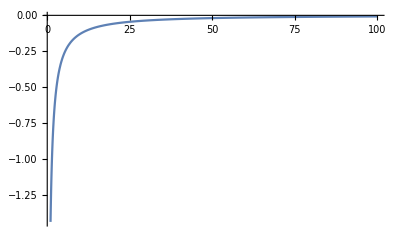

```mathematica
Plot[Alpha[Uc][[1]],{Uc,1,100},PlotRange->Full,PerformanceGoal->"Quality"]
```

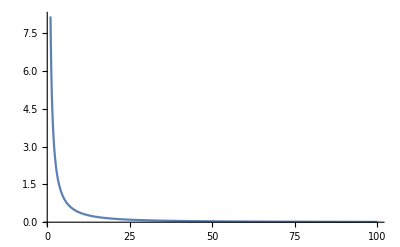

```mathematica
Plot[Alpha[Uc][[2]],{Uc,1,100},PlotRange->Full,PerformanceGoal->"Quality"]
```

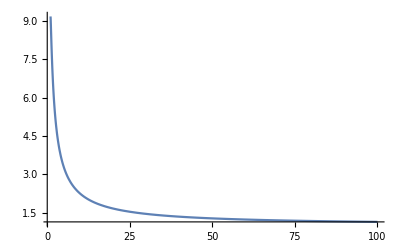

```mathematica
Plot[Alpha[Uc][[3]],{Uc,1,100},PlotRange->Full,PerformanceGoal->"Quality"]
```